```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

some other stoichiometric matrices

```mathematica
stoichioforecoli=Drop[Import["../210324_disc_time_windows_and_OR_model/e_coli_core_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforecoli
```

SparseArray[…]

```mathematica
stoichioforhomosapiensbig=Import["../210324_disc_time_windows_and_OR_model/Recon3D_stoichiomat_noheaders.mx"];
SparseArray@stoichioforhomosapiensbig
```

SparseArray[…]

thesis data set

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

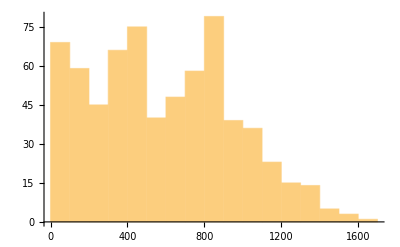

586.809

675

```mathematica
sequencesizes=Values@Counts@datafull[[All,2]];
Histogram@sequencesizes
N@Mean@sequencesizes
Length@sequencesizes
```

system cartoon

boundary (resource) restriction

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=1008;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors1=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}];
```

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=1008;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors2=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}];
```

some other stoichiometric matrix trials

```mathematica
syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,190]
```

{{2.9211×10^-16,2.70647×10^-16,2.70647×10^-16,2.63401×10^-16,2.68438×10^-16,2.66989×10^-16,2.69817×10^-16,2.69817×10^-16,2.67937×10^-16,3.83371×10^-16,988,1.38774×10^-16,5.50151×10^-16,3.45629×10^-16,1.85591×10^-16,1.31663×10^-15,3.53718×10^-16,3.03858×10^-16,2.37299×10^-16,2.64935×10^-16,3.67522×10^-16},188,{1}}
 |  |  |  |

```mathematica
Dimensions@%434
Min@(Flatten[RealDigits[%434],1][[All,2]])
```

{190,1008}

-16

```mathematica
Counts@Flatten[RealDigits[%434],1][[All,2]]
```

<|-15→188448,3→380,-14→2511,-16→181|>

```mathematica
stoichiometricmatrix=stoichioforecoli;
metabolites=72;
fluxexchanges=95;
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,190]
```

{1}
 |  |  |  |

```mathematica
Dimensions@%446
Min@(Flatten[RealDigits[%446],1][[All,2]])
```

{190,95}

-323

```mathematica
Counts@Flatten[RealDigits[%446],1][[All,2]]
```

<|-323→13323,-12→1286,-27→197,-26→94,-13→510,-25→26,3→200,-28→91,-44→2,-11→968,-14→117,-10→657,-15→17,-9→456,-29→56,-24→16,-30→25,-31→2,-23→3,-16→4|>

```mathematica
stoichiometricmatrix=stoichioforhomosapiensbig;
metabolites=5835;
fluxexchanges=10600;
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,190]
```

{{2.53364×10^-15,1.68503×10^-15,6.86818×10^-15,1.04584×10^-15,9.06967×10^-15,8.84261×10^-16,1.90378×10^-15,3.69014×10^-15,1.29822×10^-15,9.87755×10^-16,10580,1.11009×10^-15,1.10603×10^-15,2.62226×10^-15,5.11137×10^-15,3.08151×10^-15,2.45698×10^-15,1.69872×10^-15,1.67636×10^-15,1.5274×10^-15,2.45698×10^-15},188,{1}}
 |  |  |  |

```mathematica
Dimensions@%465
Min@(Flatten[RealDigits[%465],1][[All,2]])
```

{190,10600}

-20

```mathematica
Counts@Flatten[RealDigits[%465],1][[All,2]]
```

<|-14→629316,-15→358108,-13→359256,-8→46160,-12→32377,3→41138,-7→52412,-6→17354,-5→2190,-4→323,2→1977,-16→342291,-11→4241,-9→30126,-10→13272,0→83,-17→60496,1→108,-18→12707,-1→71,-3→46,-2→17,-19→9895,-20→36|>